```mathematica
m=1;
M=1;
l=1;
L=1;
g=10;
x1=l Sin[θ[t]];
y1=-l Cos[θ[t]];
x2=x1+L Sin[θ[t]+α[t]];
y2=y1-L Cos[θ[t]+α[t]];
V=m g y1+M g y2;
vx1=D[x1,t];
vy1=D[y1,t];
vx2=D[x2,t];
vy2=D[y2,t];
T=(m/2)(vx1^2+vy1^2)+(M/2)(vx2^2+vy2^2);
ℒ=T-V;
time=60;
Needs["VariationalMethods`"]
eqs=EulerEquations[ℒ,{θ[t],α[t]},t];
s=NDSolve[{eqs,θ[0]==Pi/4,α[0]==Pi/8,θ'[0]==0,α'[0]==0},{θ,α},{t,0,time}]

"Double Pendulum Motion:"
plt=Plot[-l-L-2,{x,-l-L-0.5-M/10,l+L+0.5+M/10},PlotRange->{-l-L-0.5-M/10,l+L+M/10}];
Animate[Show[plt,Graphics[{Line[{{0,0},{l*Sin[θ[t]],-l*Cos[θ[t]]}}]}],Graphics[{Line[{{l*Sin[θ[t]],-l*Cos[θ[t]]},{l*Sin[θ[t]]+L*Sin[θ[t]+α[t]],-l*Cos[θ[t]]-L*Cos[θ[t]+α[t]]}}]}],Graphics[{Red,Ball[{l*Sin[θ[t]],-l*Cos[θ[t]]},m/10]}],Graphics[{Red,Ball[{l*Sin[θ[t]]+L*Sin[θ[t]+α[t]],-l*Cos[θ[t]]-L*Cos[θ[t]+α[t]]},M/10]}],AspectRatio->Automatic]/.s,{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```

{{θ→InterpolatingFunction[{{0., 60.}}, <>],α→InterpolatingFunction[{{0., 60.}}, <>]}}

Double Pendulum Motion:

{{θ→InterpolatingFunction[{{0, 60.000000000000000000}}, <>],α→InterpolatingFunction[{{0, 60.000000000000000000}}, <>],pθ→InterpolatingFunction[{{0, 60.000000000000000000}}, <>],pα→InterpolatingFunction[{{0, 60.000000000000000000}}, <>]}}

Double Pendulum Phase Space Trajectory:

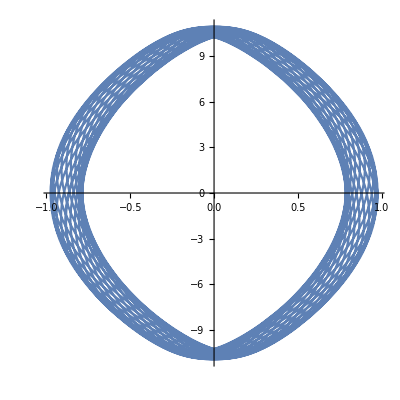

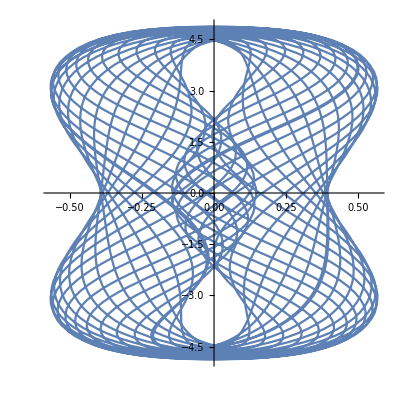

Double Pendulum Motion:

```mathematica
m=1;
M=1;
l=1;
L=1;
g=10;
ℋ=((M L^2+(m+M)l^2+2M l L Cos[α[t]])pα[t]^2-2M L(L+l Cos[α[t]])pα[t]pθ[t]-M L^2(2g l^2(m+M Sin[α[t]]^2) ((m+M)l Cos[θ[t]]+M L Cos[α[t]+θ[t]])-pθ[t]^2))/(2 l^2 L^2 M (m+M Sin[α[t]]^2));
time=60;
eq1=θ'[t]==D[ℋ,pθ[t]];
eq2=α'[t]==D[ℋ,pα[t]];
eq3=pθ'[t]==-D[ℋ,θ[t]];
eq4=pα'[t]==-D[ℋ,α[t]];
s=NDSolve[{eq1,eq2,eq3,eq4,θ[0]==Pi/4,α[0]==Pi/8,pθ[0]==0,pα[0]==0},{θ,α,pθ,pα},{t,0,time},WorkingPrecision->20]

"Double Pendulum Phase Space Trajectory:"
ParametricPlot[Evaluate[{θ[t],pθ[t]}/.s],{t,0,time},AspectRatio->1]
ParametricPlot[Evaluate[{α[t],pα[t]}/.s],{t,0,time},AspectRatio->1]

"Double Pendulum Motion:"
plt=Plot[-l-L-2,{x,-l-L-0.5-M/10,l+L+0.5+M/10},PlotRange->{-l-L-0.5-M/10,l+L+M/10}];
Animate[Show[plt,Graphics[{Line[{{0,0},{l*Sin[θ[t]],-l*Cos[θ[t]]}}]}],Graphics[{Line[{{l*Sin[θ[t]],-l*Cos[θ[t]]},{l*Sin[θ[t]]+L*Sin[θ[t]+α[t]],-l*Cos[θ[t]]-L*Cos[θ[t]+α[t]]}}]}],Graphics[{Red,Ball[{l*Sin[θ[t]],-l*Cos[θ[t]]},m/10]}],Graphics[{Red,Ball[{l*Sin[θ[t]]+L*Sin[θ[t]+α[t]],-l*Cos[θ[t]]-L*Cos[θ[t]+α[t]]},M/10]}],AspectRatio->Automatic]/.s,{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```